```mathematica
(* Taylor series expansion of Sin[x] about x = 0 up to order 5 *)
Series[Sin[x], {x, 0, 9}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^10

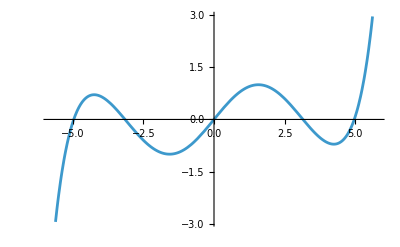

```mathematica
Plot[Evaluate[Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^10]],{x,-5.7846,5.7846}]
```

```mathematica
CoefficientList[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^10,x]
```

{0,1,0,-1/6,0,1/120,0,-1/5040,0,1/362880}

```mathematica
Total[{0,1,0,-1/6,0,1/120,0,-1/5040,0,1/362880}]
```

305353/362880

```mathematica
Plot[Evaluate[Normal[x-x^3/6+x^5/120+O[x]^6]],{x,-10.954451150103322,10.954451150103322}]
```

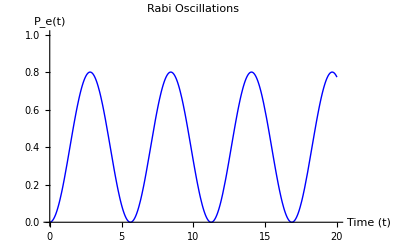

```mathematica
(*Parameters*)ΩR=1; (*Rabi frequency*)
Δ=0.5; (*Detuning*)
Ω=Sqrt[ΩR^2+Δ^2]; (*Generalized Rabi frequency*)

(*Probability of being in the excited state as a function of time*)
Pe[t_]:=(ΩR^2/Ω^2)*Sin[Ω t/2]^2

(*Plot the Rabi oscillations*)
Plot[Pe[t],{t,0,20},PlotRange->{0,1},PlotLabel->"Rabi Oscillations",AxesLabel->{"Time (t)","P_e(t)"},PlotStyle->{Thick,Blue}]
```

```mathematica
(*Unperturbed energy levels*)E1=0;
E2=Δ; (*Energy gap between the levels*)

(*Time-dependent perturbation:assume V(t)=V0 Cos[ω t]*)
V0=0.1;
ω=1;
V[t_]:=V0 Cos[ω t];

(*Hamiltonian matrix*)
H[t_]:={{E1,V[t]},{V[t],E2}}

(*Second-order energy shift using TDPT formula*)
ΔE1SecondOrder=Integrate[(Abs[V[t]]^2)/(E1-E2)*Exp[I (E1-E2) t],{t,0,Infinity},Assumptions->{Δ>0,V0>0,ω>0}]

ΔE2SecondOrder=Integrate[(Abs[V[t]]^2)/(E2-E1)*Exp[I (E2-E1) t],{t,0,Infinity},Assumptions->{Δ>0,V0>0,ω>0}]

(*Display the results*)
{ΔE1SecondOrder,ΔE2SecondOrder}
```

0.+0.0186667 ⅈ

0.+0.0186667 ⅈ

{0.+0.0186667 ⅈ,0.+0.0186667 ⅈ}

```mathematica
(* ::Section::*)(*TDPT Derivation of Energy Shifts for a Spin-1/2 System*)(*Parameters and Definitions*)ClearAll["Global`*"]
=Symbol[""]; (*Gyromagnetic ratio*)
Bz=Symbol["Bz"];
Bperp=Symbol["Bp"];
ω0=γ Bz; (*Larmor frequency*)
ωperp=Symbol["ωp"];
ħ=Symbol["ℏ"];

(*Pauli matrices for spin-1/2*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
Sx=(ħ/2) σx;
Sy=(ħ/2) σy;
Sz=(ħ/2) σz;

(*Spin ladder operators*)
Sp=Sx+I Sy;
Sm=Sx-I Sy;

(*Hamiltonian components*)
H0=-γ Bz Sz; (*Unperturbed Hamiltonian*)
Vt=-(γ Bperp/2) (Sm Exp[-I ωperp t]+Sp Exp[I ωperp t]); (*Time-dependent perturbation*)

(* ::Section::*)
(*Second-Order Energy Shift Calculation Using TDPT*)

(*Eigenstates and eigenvalues of H0*)
{vals,vecs}=Eigensystem[H0];
states=vecs;
energies=vals;

(*Define second-order TDPT energy shift function*)
secondOrderShift[stateIndex_]:=Module[{E0,psi,sum},E0=energies[[stateIndex]];(*Energy of the target state*)psi=states[[stateIndex]];(*Wavefunction of the target state*)sum=Sum[With[{E1=energies[[j]],phi=states[[j]]},If[j==stateIndex,0,(*Skip the state itself in the sum*)Integrate[(Conjugate[psi].Vt.phi/. {Conjugate[psi_].Sp.phi_->1,Conjugate[psi_].Sm.phi_->1})*Exp[I (E0-E1) t]/(E0-E1+ħ ωperp),(*TDPT second-order formula*){t,0,Infinity},Assumptions->{ωperp>0,Bz>0}   (*Assumptions for simplification*)]]],{j,1,Length[states]}           (*Sum over all intermediate states*)];
sum];

(*Calculate energy shifts for|+1/2>and|-1/2>*)
ΔEPlus=Simplify[secondOrderShift[1]];
ΔEMinus=Simplify[secondOrderShift[2]];

(* ::Section::*)
(*Display Results*)
ΔEPlus//TraditionalForm
ΔEMinus//TraditionalForm

(* ::Section::*)
(*Check for Matching with Eq.(6) and Eq.(7)*)
(*Extract and simplify final expressions*)
Simplify[ΔEPlus]
Simplify[ΔEMinus]
```

Symbol::symname: The string "" cannot be used for a symbol name. A symbol name must start with a letter followed by letters and numbers.

ConditionalExpression[(ⅈ Bp Symbol[])/((2 Bz Symbol[]-2 ωp) (ωp-Bz ℏ Symbol[])), Im(ℏ Symbol[])<0]

ConditionalExpression[(ⅈ Bp Symbol[])/(2 (Bz Symbol[]+ωp) (ωp-Bz ℏ Symbol[])), Im(ℏ Symbol[])>0]

ConditionalExpression[(ⅈ Bp Symbol[])/((-2 ωp+2 Bz Symbol[]) (ωp-Bz ℏ Symbol[])), Im[ℏ Symbol[]]<0]

ConditionalExpression[(ⅈ Bp Symbol[])/(2 (ωp+Bz Symbol[]) (ωp-Bz ℏ Symbol[])), Im[ℏ Symbol[]]>0]

```mathematica
(* ::Section::*)(*TDPT Derivation of Energy Shifts for a Spin-1/2 System*)(*Parameters and Definitions*)ClearAll["Global`*"]
=Symbol[""]; (*Gyromagnetic ratio*)
Bz=Symbol["Bz"];
Bperp=Symbol["Bp"];
ω0=γ Bz; (*Larmor frequency*)
ωperp=Symbol["ωp"];
ħ=Symbol["ℏ"];

(*Pauli matrices for spin-1/2*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
Sx=(ħ/2) σx;
Sy=(ħ/2) σy;
Sz=(ħ/2) σz;

(*Spin ladder operators*)
Sp=Sx+I Sy;
Sm=Sx-I Sy;

(*Hamiltonian components*)
H0=-γ Bz Sz; (*Unperturbed Hamiltonian*)
Vt=-(γ Bperp/2) (Sm Exp[-I ωperp t]+Sp Exp[I ωperp t]); (*Time-dependent perturbation*)

(* ::Section::*)
(*Second-Order Energy Shift Calculation Using TDPT*)

(*Eigenstates and eigenvalues of H0*)
{vals,vecs}=Eigensystem[H0];
states=vecs;
energies=vals;

(*Define second-order TDPT energy shift function*)
secondOrderShift[stateIndex_]:=Module[{E0,psi,sum},E0=energies[[stateIndex]];(*Energy of the target state*)psi=states[[stateIndex]];(*Wavefunction of the target state*)sum=Sum[With[{E1=energies[[j]],phi=states[[j]]},If[j==stateIndex,0,(*Skip the state itself in the sum*)Integrate[(Conjugate[psi].Vt.phi/. {Conjugate[psi_].Sp.phi_->1,Conjugate[psi_].Sm.phi_->1})*Exp[I (E0-E1) t]/(E0-E1+ħ ωperp),(*TDPT second-order formula*){t,0,Infinity},Assumptions->{ωperp>0,Bz>0}   (*Assumptions for simplification*)]]],{j,1,Length[states]}           (*Sum over all intermediate states*)];
sum];

(*Calculate energy shifts for|+1/2>and|-1/2>*)
ΔEPlus=Simplify[secondOrderShift[1]];
ΔEMinus=Simplify[secondOrderShift[2]];

(* ::Section::*)
(*Display Results*)
ΔEPlus//TraditionalForm
ΔEMinus//TraditionalForm

(* ::Section::*)
(*Check for Matching with Eq.(6) and Eq.(7)*)
(*Extract and simplify final expressions*)
Simplify[ΔEPlus]
Simplify[ΔEMinus](* ::Section::*)(*TDPT Derivation of Energy Shifts for a Spin-1/2 System*)(*Parameters and Definitions*)ClearAll["Global`*"]
=Symbol["TemplateBox[<|\"boxes\" -> FormBox[\"γ\", TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\gamma\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"]"]; (*Gyromagnetic ratio*)
Bz=Symbol["Bz"];
Bperp=Symbol["Bp"];
ω0=γ Bz; (*Larmor frequency*)
ωperp=Symbol["ωp"];
ħ=Symbol["ℏ"];

(*Pauli matrices for spin-1/2*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
Sx=(ħ/2) σx;
Sy=(ħ/2) σy;
Sz=(ħ/2) σz;

(*Spin ladder operators*)
Sp=Sx+I Sy;
Sm=Sx-I Sy;

(*Hamiltonian components*)
H0=-γ Bz Sz; (*Unperturbed Hamiltonian*)
Vt=-(γ Bperp/2) (Sm Exp[-I ωperp t]+Sp Exp[I ωperp t]); (*Time-dependent perturbation*)

(* ::Section::*)
(*Second-Order Energy Shift Calculation Using TDPT*)

(*Eigenstates and eigenvalues of H0*)
{vals,vecs}=Eigensystem[H0];
states=vecs;
energies=vals;

(*Define second-order TDPT energy shift function*)
secondOrderShift[stateIndex_]:=Module[{E0,psi,sum},E0=energies[[stateIndex]];(*Energy of the target state*)psi=states[[stateIndex]];(*Wavefunction of the target state*)sum=Sum[With[{E1=energies[[j]],phi=states[[j]]},If[j==stateIndex,0,(*Skip the state itself in the sum*)Integrate[(Conjugate[psi].Vt.phi/. {Conjugate[psi_].Sp.phi_->1,Conjugate[psi_].Sm.phi_->1})*Exp[I (E0-E1) t]/(E0-E1+ħ ωperp),(*TDPT second-order formula*){t,0,Infinity},Assumptions->{ωperp>0,Bz>0}   (*Assumptions for simplification*)]]],{j,1,Length[states]}           (*Sum over all intermediate states*)];
sum];

(*Calculate energy shifts for|+1/2>and|-1/2>*)
ΔEPlus=Simplify[secondOrderShift[1]];
ΔEMinus=Simplify[secondOrderShift[2]];

(* ::Section::*)
(*Display Results*)
ΔEPlus//TraditionalForm
ΔEMinus//TraditionalForm

(* ::Section::*)
(*Check for Matching with Eq.(6) and Eq.(7)*)
(*Extract and simplify final expressions*)
Simplify[ΔEPlus]
Simplify[ΔEMinus](* ::Section::*)(*TDPT Derivation of Energy Shifts for a Spin-1/2 System*)(*Parameters and Definitions*)ClearAll["Global`*"]
=Symbol["TemplateBox[<|\"boxes\" -> FormBox[\"γ\", TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\gamma\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"]"]; (*Gyromagnetic ratio*)
Bz=Symbol["Bz"];
Bperp=Symbol["Bp"];
ω0=γ Bz; (*Larmor frequency*)
ωperp=Symbol["ωp"];
ħ=Symbol["ℏ"];

(*Pauli matrices for spin-1/2*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
Sx=(ħ/2) σx;
Sy=(ħ/2) σy;
Sz=(ħ/2) σz;

(*Spin ladder operators*)
Sp=Sx+I Sy;
Sm=Sx-I Sy;

(*Hamiltonian components*)
H0=-γ Bz Sz; (*Unperturbed Hamiltonian*)
Vt=-(γ Bperp/2) (Sm Exp[-I ωperp t]+Sp Exp[I ωperp t]); (*Time-dependent perturbation*)

(* ::Section::*)
(*Second-Order Energy Shift Calculation Using TDPT*)

(*Eigenstates and eigenvalues of H0*)
{vals,vecs}=Eigensystem[H0];
states=vecs;
energies=vals;

(*Define second-order TDPT energy shift function*)
secondOrderShift[stateIndex_]:=Module[{E0,psi,sum},E0=energies[[stateIndex]];(*Energy of the target state*)psi=states[[stateIndex]];(*Wavefunction of the target state*)sum=Sum[With[{E1=energies[[j]],phi=states[[j]]},If[j==stateIndex,0,(*Skip the state itself in the sum*)Integrate[(Conjugate[psi].Vt.phi/. {Conjugate[psi_].Sp.phi_->1,Conjugate[psi_].Sm.phi_->1})*Exp[I (E0-E1) t]/(E0-E1+ħ ωperp),(*TDPT second-order formula*){t,0,Infinity},Assumptions->{ωperp>0,Bz>0}   (*Assumptions for simplification*)]]],{j,1,Length[states]}           (*Sum over all intermediate states*)];
sum];

(*Calculate energy shifts for|+1/2>and|-1/2>*)
ΔEPlus=Simplify[secondOrderShift[1]];
ΔEMinus=Simplify[secondOrderShift[2]];

(* ::Section::*)
(*Display Results*)
ΔEPlus//TraditionalForm
ΔEMinus//TraditionalForm

(* ::Section::*)
(*Check for Matching with Eq.(6) and Eq.(7)*)
(*Extract and simplify final expressions*)
Simplify[ΔEPlus]
Simplify[ΔEMinus](* ::Section::*)(*TDPT Derivation of Energy Shifts for a Spin-1/2 System*)(*Parameters and Definitions*)ClearAll["Global`*"]
=Symbol["TemplateBox[<|\"boxes\" -> FormBox[\"γ\", TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\gamma\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"]"]; (*Gyromagnetic ratio*)
Bz=Symbol["Bz"];
Bperp=Symbol["Bp"];
ω0=γ Bz; (*Larmor frequency*)
ωperp=Symbol["ωp"];
ħ=Symbol["ℏ"];

(*Pauli matrices for spin-1/2*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
Sx=(ħ/2) σx;
Sy=(ħ/2) σy;
Sz=(ħ/2) σz;

(*Spin ladder operators*)
Sp=Sx+I Sy;
Sm=Sx-I Sy;

(*Hamiltonian components*)
H0=-γ Bz Sz; (*Unperturbed Hamiltonian*)
Vt=-(γ Bperp/2) (Sm Exp[-I ωperp t]+Sp Exp[I ωperp t]); (*Time-dependent perturbation*)

(* ::Section::*)
(*Second-Order Energy Shift Calculation Using TDPT*)

(*Eigenstates and eigenvalues of H0*)
{vals,vecs}=Eigensystem[H0];
states=vecs;
energies=vals;

(*Define second-order TDPT energy shift function*)
secondOrderShift[stateIndex_]:=Module[{E0,psi,sum},E0=energies[[stateIndex]];(*Energy of the target state*)psi=states[[stateIndex]];(*Wavefunction of the target state*)sum=Sum[With[{E1=energies[[j]],phi=states[[j]]},If[j==stateIndex,0,(*Skip the state itself in the sum*)Integrate[(Conjugate[psi].Vt.phi/. {Conjugate[psi_].Sp.phi_->1,Conjugate[psi_].Sm.phi_->1})*Exp[I (E0-E1) t]/(E0-E1+ħ ωperp),(*TDPT second-order formula*){t,0,Infinity},Assumptions->{ωperp>0,Bz>0}   (*Assumptions for simplification*)]]],{j,1,Length[states]}           (*Sum over all intermediate states*)];
sum];

(*Calculate energy shifts for|+1/2>and|-1/2>*)
ΔEPlus=Simplify[secondOrderShift[1]];
ΔEMinus=Simplify[secondOrderShift[2]];

(* ::Section::*)
(*Display Results*)
ΔEPlus//TraditionalForm
ΔEMinus//TraditionalForm

(* ::Section::*)
(*Check for Matching with Eq.(6) and Eq.(7)*)
(*Extract and simplify final expressions*)
Simplify[ΔEPlus]
Simplify[ΔEMinus](* ::Section::*)(*TDPT Derivation of Energy Shifts for a Spin-1/2 System*)(*Parameters and Definitions*)ClearAll["Global`*"]
=Symbol["TemplateBox[<|\"boxes\" -> FormBox[\"γ\", TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\gamma\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"]"]; (*Gyromagnetic ratio*)
Bz=Symbol["Bz"];
Bperp=Symbol["Bp"];
ω0=γ Bz; (*Larmor frequency*)
ωperp=Symbol["ωp"];
ħ=Symbol["ℏ"];

(*Pauli matrices for spin-1/2*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
Sx=(ħ/2) σx;
Sy=(ħ/2) σy;
Sz=(ħ/2) σz;

(*Spin ladder operators*)
Sp=Sx+I Sy;
Sm=Sx-I Sy;

(*Hamiltonian components*)
H0=-γ Bz Sz; (*Unperturbed Hamiltonian*)
Vt=-(γ Bperp/2) (Sm Exp[-I ωperp t]+Sp Exp[I ωperp t]); (*Time-dependent perturbation*)

(* ::Section::*)
(*Second-Order Energy Shift Calculation Using TDPT*)

(*Eigenstates and eigenvalues of H0*)
{vals,vecs}=Eigensystem[H0];
states=vecs;
energies=vals;

(*Define second-order TDPT energy shift function*)
secondOrderShift[stateIndex_]:=Module[{E0,psi,sum},E0=energies[[stateIndex]];(*Energy of the target state*)psi=states[[stateIndex]];(*Wavefunction of the target state*)sum=Sum[With[{E1=energies[[j]],phi=states[[j]]},If[j==stateIndex,0,(*Skip the state itself in the sum*)Integrate[(Conjugate[psi].Vt.phi/. {Conjugate[psi_].Sp.phi_->1,Conjugate[psi_].Sm.phi_->1})*Exp[I (E0-E1) t]/(E0-E1+ħ ωperp),(*TDPT second-order formula*){t,0,Infinity},Assumptions->{ωperp>0,Bz>0}   (*Assumptions for simplification*)]]],{j,1,Length[states]}           (*Sum over all intermediate states*)];
sum];

(*Calculate energy shifts for|+1/2>and|-1/2>*)
ΔEPlus=Simplify[secondOrderShift[1]];
ΔEMinus=Simplify[secondOrderShift[2]];

(* ::Section::*)
(*Display Results*)
ΔEPlus//TraditionalForm
ΔEMinus//TraditionalForm

(* ::Section::*)
(*Check for Matching with Eq.(6) and Eq.(7)*)
(*Extract and simplify final expressions*)
Simplify[ΔEPlus]
Simplify[ΔEMinus](* ::Section::*)(*TDPT Derivation of Energy Shifts for a Spin-1/2 System*)(*Parameters and Definitions*)ClearAll["Global`*"]
=Symbol["TemplateBox[<|\"boxes\" -> FormBox[\"γ\", TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\gamma\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"]"]; (*Gyromagnetic ratio*)
Bz=Symbol["Bz"];
Bperp=Symbol["Bp"];
ω0=γ Bz; (*Larmor frequency*)
ωperp=Symbol["ωp"];
ħ=Symbol["ℏ"];

(*Pauli matrices for spin-1/2*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
Sx=(ħ/2) σx;
Sy=(ħ/2) σy;
Sz=(ħ/2) σz;

(*Spin ladder operators*)
Sp=Sx+I Sy;
Sm=Sx-I Sy;

(*Hamiltonian components*)
H0=-γ Bz Sz; (*Unperturbed Hamiltonian*)
Vt=-(γ Bperp/2) (Sm Exp[-I ωperp t]+Sp Exp[I ωperp t]); (*Time-dependent perturbation*)

(* ::Section::*)
(*Second-Order Energy Shift Calculation Using TDPT*)

(*Eigenstates and eigenvalues of H0*)
{vals,vecs}=Eigensystem[H0];
states=vecs;
energies=vals;

(*Define second-order TDPT energy shift function*)
secondOrderShift[stateIndex_]:=Module[{E0,psi,sum},E0=energies[[stateIndex]];(*Energy of the target state*)psi=states[[stateIndex]];(*Wavefunction of the target state*)sum=Sum[With[{E1=energies[[j]],phi=states[[j]]},If[j==stateIndex,0,(*Skip the state itself in the sum*)Integrate[(Conjugate[psi].
```

```mathematica
Vt.phi/. {Conjugate[psi_].Sp.phi_->1,Conjugate[psi_].Sm.phi_->1})*Exp[I (E0-E1) t]/(E0-E1+ħ ωperp),(*TDPT second-order formula*){t,0,Infinity},Assumptions->{ωperp>0,Bz>0}   (*Assumptions for simplification*)]]],{j,1,Length[states]}           (*Sum over all intermediate states*)];
sum];

(*Calculate energy shifts for|+1/2>and|-1/2>*)
ΔEPlus=Simplify[secondOrderShift[1]];
ΔEMinus=Simplify[secondOrderShift[2]];

(* ::Section::*)
(*Display Results*)
ΔEPlus//TraditionalForm
ΔEMinus//TraditionalForm

(* ::Section::*)
(*Check for Matching with Eq.(6) and Eq.(7)*)
(*Extract and simplify final expressions*)
Simplify[ΔEPlus]
Simplify[ΔEMinus]
```

```mathematica
(*Define time-dependent variables*)vars={L[t],F[t],G[t],H[t],\[OverBar]L[t],\[OverBar]F[t],\[OverBar]G[t],\[OverBar]H[t]};

(*Define parameters*)
delta[t_]:=δ[t];
gamma1[t_]:=γ1[t];
gamma2[t_]:=γ2[t];
Omega1[t_]:=Ω1[t];
Omega2[t_]:=Ω2[t];

eqns={(*System for U*)I D[L[t],t]==(delta[t]-I gamma2[t]/2) L[t]-Omega1[t] F[t],I D[F[t],t]==-Omega2[t] L[t]-I gamma1[t]/2 F[t],I D[G[t],t]==(delta[t]-I gamma2[t]/2) G[t]-Omega1[t] H[t],I D[H[t],t]==-Omega2[t] G[t]-I gamma1[t]/2 H[t],(*System for U bar*)I D[\[OverBar]L[t],t]==(delta[t]+I gamma2[t]/2) \[OverBar]L[t]-Conjugate[Omega2[t]] \[OverBar]F[t],I D[\[OverBar]F[t],t]==-Conjugate[Omega1[t]] \[OverBar]L[t]+I gamma1[t]/2 \[OverBar]F[t],I D[\[OverBar]G[t],t]==(delta[t]+I gamma2[t]/2) \[OverBar]G[t]-Conjugate[Omega2[t]] \[OverBar]H[t],I D[\[OverBar]H[t],t]==-Conjugate[Omega1[t]] \[OverBar]G[t]+I gamma1[t]/2 \[OverBar]H[t],(*Initial conditions*)L[0]==1,F[0]==0,G[0]==0,H[0]==1,\[OverBar]L[0]==1,\[OverBar]F[0]==0,\[OverBar]G[0]==0,\[OverBar]H[0]==1};
```

Syntax::sntxb: Expression cannot begin with "\[OverBar]L[t]".

```mathematica
constraints={L[t] Conjugate[\[OverBar]L[t]]+F[t] Conjugate[\[OverBar]F[t]]==1,G[t] Conjugate[\[OverBar]G[t]]+H[t] Conjugate[\[OverBar]H[t]]==1,G[t] Conjugate[\[OverBar]L[t]]+H[t] Conjugate[\[OverBar]F[t]]==0,L[t] Conjugate[\[OverBar]G[t]]+F[t] Conjugate[\[OverBar]H[t]]==0};
```

```mathematica
(*Solve the system numerically*)sol=NDSolveValue[eqns,{L,F,G,H},{t,0,T}];
```

NDSolveValue::underdet: There are more dependent variables, {F[t],G[t],L[t],γ1[t],γ2[t],δ[t],Ω1[t],Ω2[t]}, than equations, so the system is underdetermined.